```mathematica
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
myRule=Sqrt[x_^2]->x;
```

```mathematica
f=1/Sqrt[a^2];
f/.myRule
```

1/(√(a^2))

```mathematica
FullForm[a+b]
```

Plus[a,b]

```mathematica
FullForm[f]
```

Power[Power[a,2],Rational[-1,2]]

```mathematica
Head[a+b]
```

Plus

```mathematica
Head[f]
```

Power

```mathematica
Head[Plus]
```

Symbol

```mathematica
FullForm[Subtract[a,b]]
```

Plus[a,Times[-1,b]]

```mathematica
FullForm[Divide[a,b]]
```

Times[a,Power[b,-1]]

```mathematica
FullForm[Sqrt[a]]
```

Power[a,Rational[1,2]]

```mathematica
FullForm[a->b]
```

Rule[a,b]

```mathematica
Clear[f];
FullForm[f[a]/.a->b]
```

f[b]

```mathematica
expr=FullForm[Hold[f[a]/.a->b]]
```

Hold[ReplaceAll[f[a],Rule[a,b]]]

```mathematica
ReleaseHold[expr]
```

f[b]

```mathematica
1+1
```

2

```mathematica
Hold[1+1]
```

Hold[1+1]

```mathematica
HoldForm[1+1]
```

1+1

```mathematica
a x^2+b x + c
```

c+b x+a x^2

```mathematica
HoldForm[a x^2+b x + c]
```

a x^2+b x+c

```mathematica
FullForm[a-2 b]
```

Plus[a,Times[-2,b]]

```mathematica
FullForm[a/b]
```

Times[a,Power[b,-1]]

```mathematica
FullForm[a==b==c]
```

Equal[a,b,c]

```mathematica
FullForm[a___]
```

Pattern[a,BlankNullSequence[]]

```mathematica
Head[Symbol]
```

Symbol

```mathematica
Head[1]
```

Integer

```mathematica
Head[Integer]
```

Symbol

```mathematica
AtomQ/@{Ψ,"blessed be the meek",-2,π,1/3,1+Iπ}
```

{True,True,True,True,True,False}

```mathematica
FullForm[1+Iπ]
```

Plus[1,I\[Pi]]

```mathematica
{FullForm[I],FullForm[Pi]}
```

{Complex[0,1],Pi}

```mathematica
{Head[I],Head[Pi]}
```

{Complex,Symbol}

```mathematica
Clear[a,b,c,x,f];
f=a x^2+b x +c;
```

```mathematica
FullForm[f]
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

```mathematica
Head[f]
```

Plus

```mathematica
Table[Part[f,n],{n,0,3}]
```

{Plus,c,b x,a x^2}

```mathematica
{First[f],Last[f]}
```

{c,a x^2}

```mathematica
(*counting from the end*)
{Part[f,-1],Part[f,-2]}
```

{a x^2,b x}

```mathematica
FullForm[Part[f,3]]
```

Times[a,Power[x,2]]

```mathematica
(*first and third parts*)
Part[f,{1,3}]
```

c+a x^2

```mathematica
(*second part of third part*)
Part[f,3,2]
```

x^2

```mathematica
(*complete addresses for occurrences of x*)
Position[f,x]
```

{{2,2},{3,2,1}}

```mathematica
Part[f,2,2]
```

x

```mathematica
ReplacePart[f,"(x used to be here)",{3,2,1}]
```

(x used to be here)^2 a+c+b x

```mathematica
f
```

c+b x+a x^2

```mathematica
f[[2,1]]=bnew;
f
```

c+bnew x+a x^2

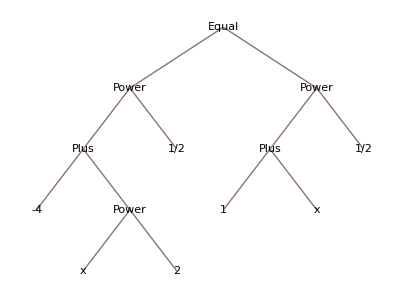

```mathematica
TreeForm[√(x^2-4)==√(x+1)]
```

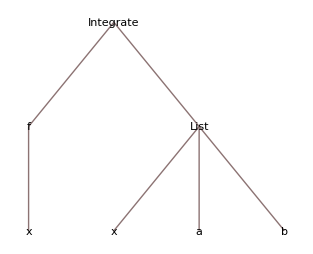

```mathematica
Clear[f];
expr=Integrate[f[x],{x,a,b}];
TreeForm[expr]
```

```mathematica
FullForm[expr]
```

Integrate[f[x],List[x,a,b]]

```mathematica
Part[expr,2,3]
```

b

```mathematica
Attributes/@{Symbol,String,Integer,Rational,Real,Complex}
```

{{Locked,Protected},{Protected},{Protected},{Protected},{Protected},{Protected}}

```mathematica
Attributes/@{Plus,Times,Power}
```

{{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected},{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected},{Listable,NumericFunction,OneIdentity,Protected}}

```mathematica
Clear[f];
f[x_]:=Sin[x]/x
```

```mathematica
f[{1,2,3,4,5}]
```

{Sin[1],Sin[2]/2,Sin[3]/3,Sin[4]/4,Sin[5]/5}

```mathematica
f/@{1,2}
```

{Sin[1],Sin[2]/2}

```mathematica
Clear[a,m,x,y,z];
a=ℏ^2/(2 m)ψ[x,y,z]
```

(ℏ^2 ψ[x,y,z])/(2 m)

```mathematica
Dt[a]
```

-(ℏ^2 Dt[m] ψ[x,y,z])/(2 m^2)+(ℏ Dt[ℏ] ψ[x,y,z])/m+(ℏ^2 (Dt[z] ψ^(0,0,1)[x,y,z]+Dt[y] ψ^(0,1,0)[x,y,z]+Dt[x] ψ^(1,0,0)[x,y,z]))/(2 m)

```mathematica
SetAttributes[{ℏ,m},Constant];
```

```mathematica
Dt[a]
```

(ℏ^2 (Dt[z] ψ^(0,0,1)[x,y,z]+Dt[y] ψ^(0,1,0)[x,y,z]+Dt[x] ψ^(1,0,0)[x,y,z]))/(2 m)

```mathematica
Clear[m]
?m
```

```mathematica
ClearAll[m]
?m
```

```mathematica
ClearAll[f,a,b];
SetAttributes[f,{Listable,OneIdentity,Flat}];
f[a_,b_]:=a⊗b
```

```mathematica
f[a,b]
```

a⊗b

```mathematica
f[a,b,c]
```

a⊗(b⊗c)

```mathematica
f[c,f[a,b]]
```

c⊗(a⊗b)

```mathematica
f[a,{b,c,d}]
```

{a⊗b,a⊗c,a⊗d}

```mathematica
f[{a,b},{c,d}]
```

{a⊗c,b⊗d}

```mathematica
a={1,2,3,4,5,6,7,8,9,10};
Head[a]
```

List

```mathematica
FullForm[a]
```

List[1,2,3,4,5,6,7,8,9,10]

```mathematica
a/.List->Plus
```

55

```mathematica
{3,η[{b,c,d}],-7,f+g}/.List->Plus
```

-4+f+g+η[b+c+d]

```mathematica
Apply[Plus,a]
```

55

```mathematica
Plus@@a
```

55

```mathematica
Plus@{3,η[{b,c,d}],-7,f+g}
```

{3,η[{b,c,d}],-7,f+g}

```mathematica
somefunction@@a
```

somefunction[1,2,3,4,5,6,7,8,9,10]

```mathematica
Clear[x,y,f];
rule1=y->f[x];
```

```mathematica
rule1
```

y→f[x]

```mathematica
FullForm[rule1]
```

Rule[y,f[x]]

```mathematica
rule1/.Rule->Equal
```

y==f[x]

```mathematica
eq1=lhs==rhs
```

lhs==rhs

```mathematica
eq1^2
```

(lhs==rhs)^2

```mathematica
FullForm[eq1]
```

Equal[lhs,rhs]

```mathematica
FullForm[eq1^2]
```

Power[Equal[lhs,rhs],2]

```mathematica
Clear[f,x,a];
f=x+a
```

a+x

```mathematica
f^2
```

(a+x)^2

```mathematica
Thread[#^2&eq1,Equal]
```

lhs (#^2&)==rhs (#^2&)

```mathematica
Thread[Power[eq1,2],Equal]
```

lhs^2==rhs^2

```mathematica
Thread[eq1^2,Equal]
```

lhs^2==rhs^2

```mathematica
list1={lhs1,lhs2,lhs3};
list2={rhs1,rhs2,rhs3};
```

```mathematica
list1==list2
```

{lhs1,lhs2,lhs3}=={rhs1,rhs2,rhs3}

```mathematica
Thread[list1==list2]
```

{lhs1==rhs1,lhs2==rhs2,lhs3==rhs3}

```mathematica
#^2&/@eq1
```

lhs^2==rhs^2

```mathematica
Clear[f];
Thread[f[eq1],Equal]/.f[x_]->x^3
```

lhs^3==rhs^3

```mathematica
Thread[Subtract[Thread[Power[Thread[Sqrt[eq1],Equal],2],Equal],rhs],Equal]
```

lhs-rhs==0

```mathematica
eqs={
Subscript[p, i]==Subscript[p, f]+K,
Subscript[p, e] Cos[ϕ]==Subscript[p, i]-Subscript[p, f] Cos[θ],
Subscript[p, e] Sin[ϕ]==Subscript[p, f] Sin[θ],
Subscript[p, e]^2==(Subscript[m, e]+K)^2-Subscript[m, e]^2
}
```

{p_i==K+p_f,Cos[ϕ] p_e==-Cos[θ] p_f+p_i,Sin[ϕ] p_e==Sin[θ] p_f,p_e^2==-m_e^2+(K+m_e)^2}

```mathematica
Solve[eqs,{Subscript[p, f],Subscript[p, e],K,ϕ}]
```

```mathematica
Eliminate[eqs,ϕ]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

2 K m_e==-K^2+p_e^2&&Sin[θ]^2 p_f^2==-K^2+p_e^2-2 K p_f+2 K Cos[θ] p_f-p_f^2+2 Cos[θ] p_f^2-Cos[θ]^2 p_f^2&&(Sin[θ] (K-2 K Cos[θ]+K Cos[θ]^2+K Sin[θ]^2+2 m_e-4 Cos[θ] m_e+2 Cos[θ]^2 m_e+2 Sin[θ]^2 m_e) p_f^2)/p_e==Sin[θ] p_e (2 m_e-2 p_f+2 Cos[θ] p_f)&&p_i==K+p_f

```mathematica
#^2&/@eqs⟦2⟧/.Equal->Subtract
```

Cos[ϕ]^2 p_e^2-(-Cos[θ] p_f+p_i)^2

```mathematica
((#^2&/@ eqs⟦3⟧)/.Equal->Subtract)
```

Sin[ϕ]^2 p_e^2-Sin[θ]^2 p_f^2

```mathematica
((#^2&/@ eqs⟦2⟧)/.Equal->Subtract)+((#^2&/@ eqs⟦3⟧)/.Equal->Subtract)==0
```

Cos[ϕ]^2 p_e^2+Sin[ϕ]^2 p_e^2-Sin[θ]^2 p_f^2-(-Cos[θ] p_f+p_i)^2==0

```mathematica
eq1=((#^2&/@ eqs⟦2⟧)/.Equal->Subtract)+((#^2&/@ eqs⟦3⟧)/.Equal->Subtract)==0//Simplify
```

p_e^2+2 Cos[θ] p_f p_i==p_f^2+p_i^2

```mathematica
newEqs={eq1,eqs⟦1⟧,eqs⟦4⟧}
```

{p_e^2+2 Cos[θ] p_f p_i==p_f^2+p_i^2,p_i==K+p_f,p_e^2==-m_e^2+(K+m_e)^2}

```mathematica
sol=Solve[newEqs,{Subscript[p, f],Subscript[p, e],K}]
```

{{p_f→(m_e p_i)/(m_e+p_i-Cos[θ] p_i),p_e→-(ⅈ √(-1+Cos[θ]) p_i √(2 m_e^2+2 m_e p_i-2 Cos[θ] m_e p_i+p_i^2-Cos[θ] p_i^2))/(√(m_e^2+2 m_e p_i-2 Cos[θ] m_e p_i+p_i^2-2 Cos[θ] p_i^2+Cos[θ]^2 p_i^2)),K→((-1+Cos[θ]) p_i^2)/(-m_e-p_i+Cos[θ] p_i)},{p_f→(m_e p_i)/(m_e+p_i-Cos[θ] p_i),p_e→(ⅈ √(-1+Cos[θ]) p_i √(2 m_e^2+2 m_e p_i-2 Cos[θ] m_e p_i+p_i^2-Cos[θ] p_i^2))/(√(m_e^2+2 m_e p_i-2 Cos[θ] m_e p_i+p_i^2-2 Cos[θ] p_i^2+Cos[θ]^2 p_i^2)),K→((-1+Cos[θ]) p_i^2)/(-m_e-p_i+Cos[θ] p_i)}}

```mathematica
sol[[1]]//Simplify
```

{p_f→(m_e p_i)/(m_e+p_i-Cos[θ] p_i),p_e→-(ⅈ √(-1+Cos[θ]) p_i √(2 m_e^2+4 Sin[θ/2]^2 m_e p_i-(-1+Cos[θ]) p_i^2))/(√((m_e-(-1+Cos[θ]) p_i)^2)),K→((-1+Cos[θ]) p_i^2)/(-m_e+(-1+Cos[θ]) p_i)}

```mathematica
1/Subscript[p, f]-1/Subscript[p, i]/.sol//Simplify
```

{(1-Cos[θ])/m_e,(1-Cos[θ])/m_e}

```mathematica
mypatt={{_Integer,_Integer,_Integer}..};
```

```mathematica
mylist= { {1,2,3},{{1,2,3}}, {{1,2,3},{-5,0,8}},x,{{1,2,3},{1.,2.,3.}} };
```

```mathematica
mylist//ColumnForm
```

{1,2,3}
{{1,2,3}}
{{1,2,3},{-5,0,8}}
x
{{1,2,3},{1.,2.,3.}}

```mathematica
MatchQ[#,mypatt]&/@mylist
```

{False,True,True,False,False}

```mathematica
Cases[mylist,mypatt]
```

{{{1,2,3}},{{1,2,3},{-5,0,8}}}

```mathematica
MatchQ[a-b c,x_ - y_Times]
```

True

```mathematica
Head[b c]
```

Times

```mathematica
MatchQ[a,a_+b_.]
```

True

```mathematica
CheckPattern[data_,pattern_]:=Transpose[{data,MatchQ[#,pattern]& /@data}]//MatrixForm
```

```mathematica
MatchQ[x^2,x_^n_Rational]
```

False

```mathematica
pattern=x_^n_Rational
```

x_^n_Rational

```mathematica
data={x,a^b,x^(1/2),x^2,3,a+b^(3/4),y^π,z z^(1/8)}
```

{x,a^b,√x,x^2,3,a+b^(3/4),y^π,z^(9/8)}

```mathematica
CheckPattern[data,pattern]
```

(x | False
a^b | False
√x | True
x^2 | False
3 | False
a+b^(3/4) | False
y^π | False
z^(9/8) | True)

```mathematica
ClearAll[f];
Attributes[f]
```

{}

```mathematica
MatchQ[f[1,x],f[x_,1]]
```

False

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
MatchQ[Plus[1,x],Plus[x_,1]]
```

True

```mathematica
SetAttributes[f,Orderless]
```

```mathematica
Attributes[f]
```

{Orderless}

```mathematica
{MatchQ[f[1,x],f[x_,1]],MatchQ[f[x,1],f[x_,1]]}
```

{True,True}

```mathematica
Clear[f,a,b,c,d]
```

```mathematica
f[a,b,c,b,a]/.f[a_,a_,b___]->f[a,b]
```

f[a,b,b,c]

```mathematica
f[b,a,c,a,b]/.f[a_,a_,b___]->f[a,b]
```

f[a,b,b,c]

```mathematica
f[a,b,c,b,a]//.f[a_,a_,b___]->f[a,b]
```

f[a,b,c]

```mathematica
f[a,a,a]//.f[a_,a_,b___]->f[a,b]
```

f[a]

```mathematica
myrule=Sqrt[x_^2]->x;
```

```mathematica
FullForm[myrule]
```

Rule[Power[Power[Pattern[x,Blank[]],2],Rational[1,2]],x]

```mathematica
√(a^2)/.myrule
```

a

```mathematica
FullForm[√(a^2)]
```

Power[Power[a,2],Rational[1,2]]

```mathematica
FullForm[1/(√(a^2))]
```

Power[Power[a,2],Rational[-1,2]]

```mathematica
myrule2=(x_^n_)^m_->x^nm
```

(x_^n_)^m_→x^nm

```mathematica
FullForm[myrule2]
```

Rule[Power[Power[Pattern[x,Blank[]],Pattern[n,Blank[]]],Pattern[m,Blank[]]],Power[x,nm]]

```mathematica
{1/(√(a^2)),(8/a^6)^(1/3),((b^2 c^9)/(a^6 d^-4))^(1/3)}/.myrule2
```

{a^nm,2 a^nm,((b^2 c^9 d^4)/a^6)^(1/3)}

```mathematica
?Trace
```

```mathematica
MatchQ[((b^2 c^9)/(a^6 d^-4))^(1/3),(x_^n_)^m_]
```

False

```mathematica
Trace[((b^2 c^9)/(a^6 d^-4))^(1/3)/.myrule2]
```

{{{{1/(a^6/d^4),d^4/a^6},(b^2 c^9 d^4)/a^6,(b^2 c^9 d^4)/a^6,(b^2 c^9 d^4)/a^6},{{1/3,1/3},1/3,1/3},((b^2 c^9 d^4)/a^6)^(1/3)},{myrule2,(x_^n_)^m_→x^nm},((b^2 c^9 d^4)/a^6)^(1/3)/.(x_^n_)^m_→x^nm,((b^2 c^9 d^4)/a^6)^(1/3)}

```mathematica
FullForm[((b^2 c^9)/(a^6 d^-4))^(1/3)]
```

Power[Times[Power[a,-6],Power[b,2],Power[c,9],Power[d,4]],Rational[1,3]]

```mathematica
MatchQ[((b^2 c^9)/(a^6 d^-4))^(1/3),x_^n_]
```

True

```mathematica
myrule3 =(a_. x_^n_)^m_->a^m x^(n m);
```

```mathematica
((b^2 c^9)/(a^6 d^-4))^(1/3)//.myrule3
```

(b^(2/3) c^3 d^(4/3))/a^2

```mathematica
((b^2 c^9)/(a^6 d^-4))^(1/3)/.myrule3
```

((b^2 c^9 d^4)^(1/3))/a^2